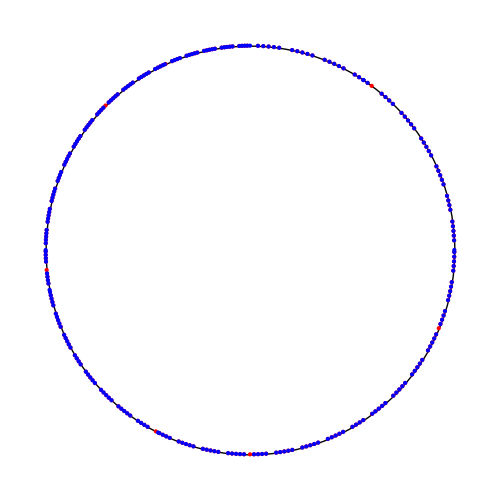

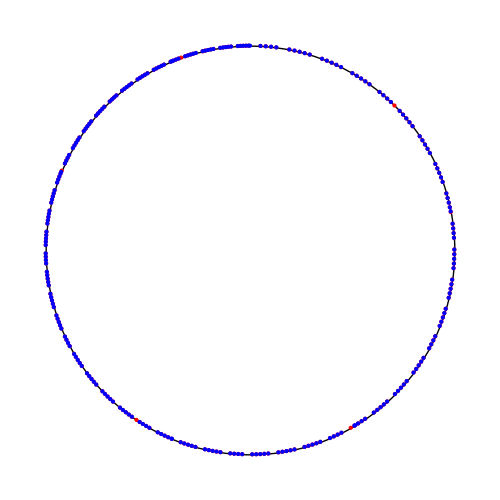

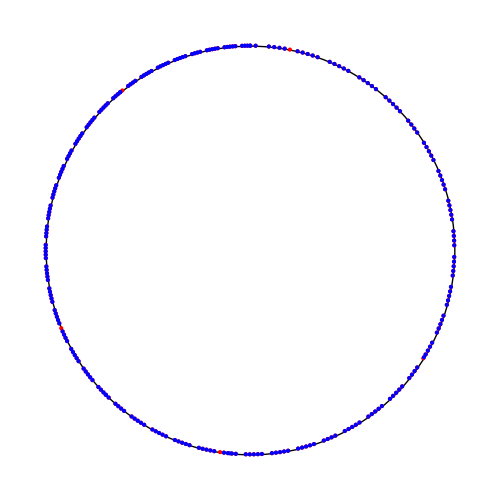

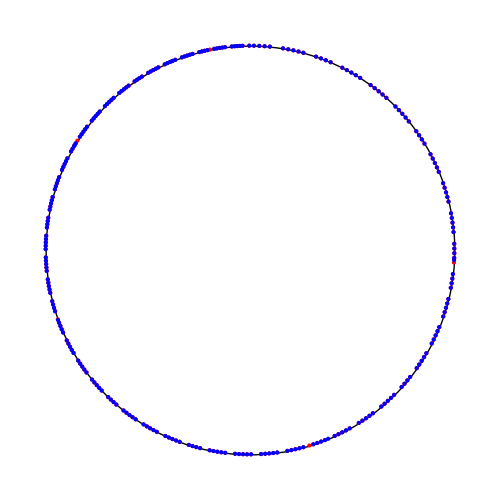

```mathematica
ClearAll["Global`*"];

r[t_]:=(
{(Sin[-t]),Cos[-t]}
);

fnfact[n_]:=n/(2^(Floor[Log[2,n]]+1)-2^Floor[Log[2,n]]);

circle[startNumber_]:=(
points=Table[Point[r[2 Pi fnfact[startNumber*3^n]]],{n,1,256}];
points2=Table[Point[r[2 Pi fnfact[(startNumber*3^n)+1]]],{n,1,256}];

Graphics[{Style[Circle[{0,0},1],Thickness[0.002]],PointSize[Large],Red,points,Blue,points2},ImageSize->500]
);

circle[1]
circle[5]
circle[7]
circle[11]
```